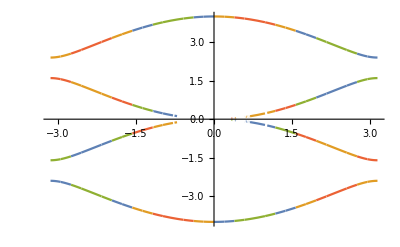

```mathematica
spectrum = (Eigenvalues[1/-ⅈ({{0, Subscript[J, 1]+Subscript[J, 2], 0, -Subscript[J, 1]-Subscript[J, 2] ⅇ^(-ⅈ k a)}, {-(Subscript[J, 1]+Subscript[J, 2]), 0, Subscript[J, 1]+Subscript[J, 2] ⅇ^(-ⅈ k a), 0}, {0, -Subscript[J, 1]-Subscript[J, 2] ⅇ^(ⅈ k a), 0, Subscript[J, 1]+Subscript[J, 2]}, {Subscript[J, 1]+Subscript[J, 2] ⅇ^(ⅈ k a), 0, -(Subscript[J, 1]+Subscript[J, 2]), 0}})] // Simplify) //. {Subscript[J, 1] -> 1.2, Subscript[J, 2]->0.8,a->1};
Plot[spectrum,{k,-π,π}]
```

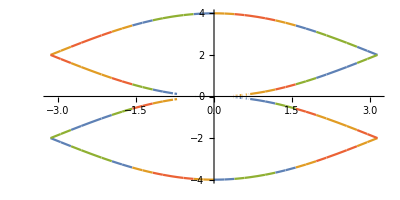

```mathematica
spectrum = (Eigenvalues[1/-ⅈ({{0, Subscript[J, 1]+Subscript[J, 2], 0, -Subscript[J, 1]-Subscript[J, 2] ⅇ^(-ⅈ k a)}, {-(Subscript[J, 1]+Subscript[J, 2]), 0, Subscript[J, 1]+Subscript[J, 2] ⅇ^(-ⅈ k a), 0}, {0, -Subscript[J, 1]-Subscript[J, 2] ⅇ^(ⅈ k a), 0, Subscript[J, 1]+Subscript[J, 2]}, {Subscript[J, 1]+Subscript[J, 2] ⅇ^(ⅈ k a), 0, -(Subscript[J, 1]+Subscript[J, 2]), 0}})] // Simplify) //. {Subscript[J, 1] -> 1, Subscript[J, 2]->1,a->1};
Plot[spectrum,{k,-π,π},AspectRatio->1/2]
```

Note: in the following code, the “1/2” factor coming with  is due to the fact that when J_1=J_2, the lattice constant shrinks to one half of the original one;  comes from the corresponding Brillouin zone folding.

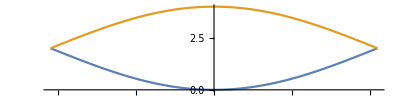

```mathematica
Plot[{2 (1-Cos[k/2]),2 (1-Cos[(k+2π)/2])},{k,-π,π},AspectRatio->1/4]
```